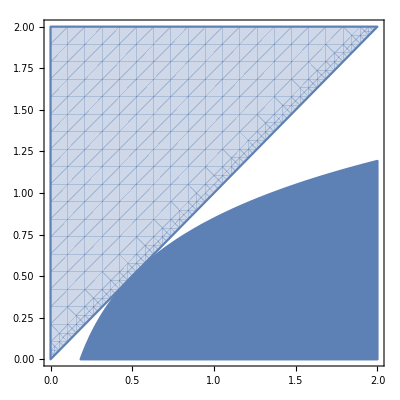

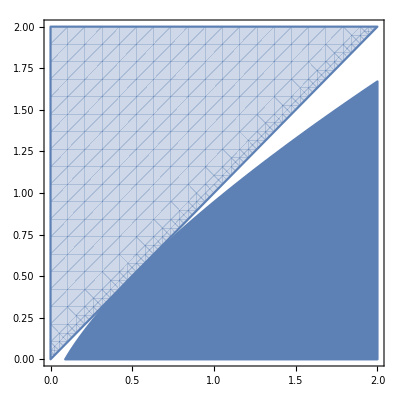

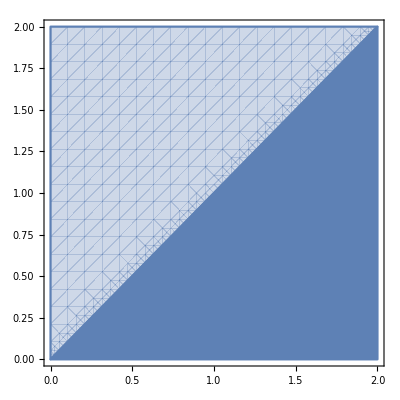

```mathematica
eps = 0.0001;
lp = 0.5;
flin[x_]:=x;
flog[x_]:=Log[x];
fpow[x_]:= x^(0.7);
lf[f_,x_,u_]:=f[u]+f'[u]*(x-u);
plt1  =Show[RegionPlot[flin[x]- lf[flin,y, lp]> 0,{x,eps,2},{y,eps,2}, PlotStyle->"Red"], RegionPlot[flin[x] - flin[y]< 0,{x,eps,2},{y,eps,2} ]];
plt2  = Show[RegionPlot[flog[x]- lf[flog,y, lp]> 0,{x,eps,2},{y,eps,2}, PlotStyle->"Red"],RegionPlot[flog[x] - flog[y]< 0,{x,eps,2},{y,eps,2}]];
plt3  = Show[RegionPlot[fpow[x]- lf[fpow,y, lp]> 0,{x,eps,2},{y,eps,2}, PlotStyle->"Red"],RegionPlot[fpow[x] - fpow[y]< 0,{x,eps,2},{y,eps,2}]];
plt2
plt3
plt1
```